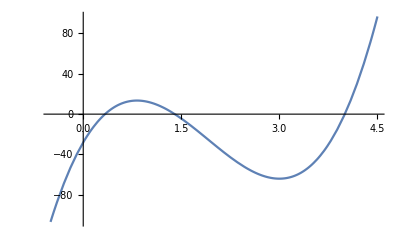

```mathematica
f[x_]:=15 x^3-86 x^2+111x-28
Plot[f[x],{x,-0.5,4.5}, AxesOrigin->{0,0}]
```

```mathematica
a=0;b=1;e=0.01;
Do[c=(a+b)/2.;
	fc=f[c];
	If[f[a]*fc<0,b=c,If[fc≠ 0,a=c]];
		If[Abs[b-a]<e||fc==0,
		Print ["x1=",c //N,", итераций " , n];
		Break[]],
{n,1,100}]
```

x1=0.335938, итераций 7

```mathematica
f[x_]:=15 x^3-86 x^2+111x-28
Plot[{f[x],f''[x]},{x,-1,5},PlotLegends->"Expressions"]
```

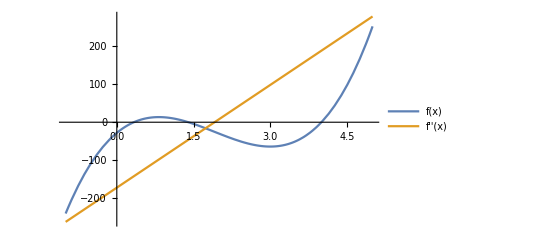

```mathematica
a=1; b=2; e=0.01; xn=1; p= 1; h=1; i;
For[i=1,Abs[h]≥e, i++, h=(15 p^3-86 p^2+111p-28)*(b-p)/(-30-(15 p^3-86 p^2+111p-28));xn= xn-h; Print[i," ",N[h], " ",N[ xn]];p=xn]
```

1 -0.285714 1.28571

2 -0.0919318 1.37765

3 -0.0184837 1.39613

4 -0.00321661 1.39935

```mathematica
Plot[{f[x],f'[x],f''[x]},{x,-1,5},PlotLegends->"Expressions"]
```

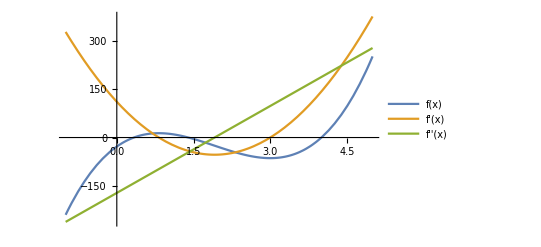

```mathematica
a=3;b=5;e=0.01;x1=b;
Do[x2=x1;
	x1=(x1-f[x1]/f'[x1])//N;
		If[Abs[x2-x1]<e,
		Print ["x=",x2 //N,", итераций " , n];
		Break[]],
{n,1,100}]
```

x=4.00181, итераций 4